# Initialize

```mathematica
ClearAll[LaserEnergy,LaserIrradiance,LaserPulseTime,LaserPower,TLE02Reflection,wl8,ref8,wl45,ref45,reflection8,reflection45,TLARCoatingA,wlA,refA,transmissionA,NumberOfMirrorsAt8,NumberOfMirrorsAt45,NumberOfLenses,LidarOutputPower,BeamDiameter,BeamIrradiance,WingSize,Reflectivity,RangeAtInsect,ScatteredRadiance,TelescopeOuterRadius,TelescopeObstructionRadius,EffectiveAperture,ProjectedSolidAngle,Throughput,ScatteredPower,AtmosphericTransmission,TelescopeReflectance,TelescopePlateTransmission,NumberOfBEFilters,NumberOfBELenses,NumberOfBEMirrors,NumberOfBEPlates,TLFLtran,wlf,traf,transmissionFL,DetectedPower,VariedAperture,x,y,TelescopeFocus,EffectiveInterestDiameter, TelescopeRatio,ProjectedSolidAngleOverFilled,PMTQE,ElectronCharge,BackgroundPower,WaveLength,PlancksConstant,SpeedOfLight,PMTCurrentSignal,PMTDarkCurrent,ElectricalBW,LensTubeObstruction,interpref8,interpref45,interprefA,DivergenceAngle,LensTubeObstruction,EffectiveApertureDiameter,DetectorArea,LambertianVegReflection,IrradianceSun,RadianceBackground,SBR,TempOfSun,AreaOfSun,k,DetectorArea,Lsun,Ωse,Esun,Lbg,Pbg,dfs,dis,QuantumEfficiencyPMT,QuantumEfficiencyWL,interpPMT,DistEarthToSun,PMTGain,LaserFreq,T,R,pulsereprate,BeamStartingDiameter,SNRv,tp,c,cv,Time,MPE,n,Cp,MPEwCp,MPEwCW,ES,PMTnoise,SNR,rng,tlr,wng,rlf,bmd,da,FOVx,FOVy,FOVd,EPL]
```

```mathematica
dfs=(*20*) 20;
dis=(*575*)600;
SetOptions[Plot,Axes->False, AxesStyle->Black,ImageSize->dis,LabelStyle->Directive[{FontFamily->"Times New Roman",dfs,Thick,Black}],PlotStyle->{Thickness[.005],ColorData["DarkRainbow"]},Frame->True];
SetOptions[SwatchLegend,LabelStyle->Directive[{FontFamily->"Times New Roman",dfs,Thick,Black}],LegendMarkerSize->{15,15}];
SetOptions[LogPlot,Axes->False,AxesStyle->Black,ImageSize->dis,LabelStyle->Directive[{FontFamily->"Times New Roman",dfs,Thick,Black}],PlotStyle->{Thickness[.004],ColorData["DarkRainbow"]},Frame->True];
SetOptions[LogLinearPlot,Axes->False,AxesStyle->Black,ImageSize->dis,LabelStyle->Directive[{FontFamily->"Times New Roman",dfs,Thick,Black}],PlotStyle->{Thickness[.004],ColorData["DarkRainbow"]},Frame->True];
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
fullfilecld="C:\\Users\\user\\OneDrive\\Documents\\Martin\\Research\\Thesis Paper\\Drafts\\figures\\rad_figs\\";
fullfileloc="C:\\Users\\user\\Documents\\Research\\Insect Lidar\\Field Tests\\Figures\\Thesis Figures\\rad_figs\\";
maindir = "H:\\scripts\\insect-lidar\\Mathematica\\"
```

# Define quantities

Colors

```mathematica
c[01]=RGBColor[18.8/100,43.5/100,61.6/100];
c[02]=RGBColor[58.4/100,38.8/100,23.9/100];
c[03]=RGBColor[62.4/100,63.5/100,63.1/100];
c[04]=RGBColor[58.0/100,41.6/100,61.2/100];
c[05]=RGBColor[84.3/100,36.1/100,33.7/100];
c[06]=RGBColor[96.1/100,71.8/100,40.8/100];
c[07]=RGBColor[50.2/100,67.8/100,43.5/100];
c[08]=RGBColor[29.0/100,50.2/100,67.1/100];
c[09]=RGBColor[56.1/100,57.3/100,56.9/100];
c[10]=RGBColor[51.4/100,34.5/100,54.5/100];
c[11]=RGBColor[81.2/100,27.5/100,23.5/100];
c[12]=RGBColor[94.9/100,67.8/100,31.0/100];
c[13]=RGBColor[42.7/100,62.7/100,36.1/100];
```

Laser Quantities

```mathematica
LaserEnergy=Quantity[3,"MicroJoules"];
LaserPulseTime=Quantity[0.6,"NanoSeconds"];
LaserPower=UnitSimplify[LaserEnergy/LaserPulseTime];
```

Optics Quantities

```mathematica
(*TLE02Reflection=Import["C:\\Martin_Tauc\\Research\\Radiometric Analysis\\E02ReflectionData.xlsx",{"Data",1,All,{3,4,5,6,7,8}}];
wl8=Drop[TLE02Reflection[[All,1]],1];
ref8=Drop[TLE02Reflection[[All,2]],1];
wl45=Drop[Drop[TLE02Reflection[[All,3]],1],-27];
ref45=Drop[Drop[TLE02Reflection[[All,4]],1],-27];
interpref8=Interpolation[Transpose[{wl8, ref8}]];
interpref45=Interpolation[Transpose[{wl45, ref45}]];
reflection8=interpref8[532]/100;
reflection45=interpref45[532]/100;*)
TLE02Reflection8=Import[maindir<>"E02ReflectionData.csv",{"Data",All,{1,2}}];
TLE02Reflection45=Import[maindir<>"E02ReflectionData.csv",{"Data",All,{3,4}}];
wl8=TLE02Reflection8[[All,1]];
ref8=TLE02Reflection8[[All,2]];
wl45=Drop[TLE02Reflection45[[All,1]],-27];
ref45=Drop[TLE02Reflection45[[All,2]],-27];
interpref8=Interpolation[Transpose[{wl8, ref8}]];
interpref45=Interpolation[Transpose[{wl45, ref45}]];
reflection8=interpref8[532]/100;
reflection45=interpref45[532]/100;
```

```mathematica
(*TLARCoatingA=Import["C:\\Martin_Tauc\\Research\\Radiometric Analysis\\A_Broadband_AR-Coating.xlsx",{"Data",1,All,{3,4}}];
wlA=Drop[TLARCoatingA[[All,1]],2];
refA=Drop[TLARCoatingA[[All,2]],2];
interprefA=Interpolation[Transpose[{wlA,refA}]];
transmissionA=(100-interprefA[532])/100;
NumberOfMirrorsAt8=1;
NumberOfMirrorsAt45=5;
NumberOfLenses=2;*)
TLARCoatingA=Import[maindir<>"A_Broadband_AR-Coating.csv",{"Data",All,All}];
wlA=TLARCoatingA[[All,1]];
refA=TLARCoatingA[[All,2]];
interprefA=Interpolation[Transpose[{wlA,refA}]];
transmissionA=(100-interprefA[532])/100;
NumberOfMirrorsAt8=1;
NumberOfMirrorsAt45=5;
NumberOfLenses=2;
```

Telescope Quantities

```mathematica
TelescopeObstructionRadius=Quantity[0.1016,"m"]/2;
LensTubeObstruction=Quantity[55.9,"mm"]*Quantity[127,"mm"];
```

Atmospheric Quantities

```mathematica
AtmosphericTransmission=0.983;
TelescopeReflectance=0.94;
TelescopePlateTransmission=0.98;
TelescopeFocus=Quantity[3048,"mm"];
NumberOfBEPlates=1;
NumberOfBEMirrors=2;
NumberOfBELenses=1;
NumberOfBEFilters=2;
(*TLFLtran=Import["C:\\Martin_Tauc\\Research\\Radiometric Analysis\\FL532-3.xlsx",{"Data",1,All,{3,4}}];
wlf=Drop[TLFLtran[[All,1]],1];
traf=Drop[TLFLtran[[All,2]],1];
transmissionFL=traf[[Flatten[Position[wlf,532.]]]][[1]]/100;*)
TLFLtran=Import[maindir<>"FL532-3.csv",{"Data",All,All}];
wlf=TLFLtran[[All,1]];
traf=TLFLtran[[All,2]];
(*transmissionFL=traf[[Flatten[Position[wlf,532.]][[1]]]]/100;*)
transmissionFL = traf[[Flatten[Position[wlf,532]][[1]]]]/100;
```

```mathematica
DetectorArea=Quantity[3.7,"mm"]*Quantity[13,"mm"];
LambertianVegReflection=0.15;
IrradianceSun=Quantity[10.83,"W/(m^2)"];
```

```mathematica
TempOfSun=Quantity[5778,"Kelvins"];
AreaOfSun=Quantity[696300,"km"]^2*Pi;
DistEarthToSun=Quantity[149.6*^6,"km"];
PlancksConstant=Quantity[6.626*^-34,"m^2*kg/s"];
SpeedOfLight=Quantity[2.998*^8,"m/s"];
k=Quantity[1.38*^-23,"J/K"];
WaveLength=Quantity[532,"nm"];
DetectorArea=Quantity[3.7*13,"mm^2"];
```

Noise Quantities

```mathematica
-Graphics-;
```

```mathematica
-Graphics-;
```

```mathematica
-Graphics-;
```

```mathematica
QuantumEfficiencyWL={200, 300, 400, 500, 600, 700, 800};
QuantumEfficiencyPMT={21.3, 22.3, 18.3, 16.6, 12.9, 3.5, 0.1};
interpPMT=Interpolation[Transpose[{QuantumEfficiencyWL,QuantumEfficiencyPMT}]];
PMTQE=interpPMT[532]/100;
ElectronCharge=Quantity[1.602*^-19,"Coulombs"];
PMTGain=4*^6;
LaserFreq=Quantity[9,"kHz"];
ElectricalBW=Quantity[100,"MHz"];
PMTDarkCurrent=Quantity[1,"nanoAmp"];
T=Quantity[300,"K"];
R=Quantity[1,"MegaOhm"];
```

Variable Quantities

```mathematica
BeamStartingDiameter=Quantity[0.0508, "m"];
(*WingSize=UnitConvert[Quantity[ws,"mm^2"],"m^2"];
RangeAtInsect=Quantity[rng,"m"];
Reflectivity=Quantity[rlf,"DimensionlessUnit"];
DivergenceAngle=Quantity[da,"Radians"];
TelescopeOuterRadius=Quantity[tlr,"m"]/2;*)
```

```mathematica
(*WingSize=UnitConvert[Quantity[25,"mm^2"],"m^2"]//N*)
(*Reflectivity=0.15;*)
(*RangeAtInsect=Quantity[100,"m"];*)
(*TelescopeOuterRadius=Quantity[0.3048,"m"]/2*)
(*Diffusivity = Quantity[Pi,"sr"]*)
```

# Equations

laser power

```mathematica
LidarOutputPower=Simplify[LaserPower*reflection8^NumberOfMirrorsAt8*reflection45^NumberOfMirrorsAt45*transmissionA^NumberOfLenses]
```

4789.88 W

beam profile

```mathematica
BeamDiameter=RangeAtInsect*2*Quantity[Tan[DivergenceAngle],"DimensionlessUnit"]+BeamStartingDiameter
BeamIrradiance=LidarOutputPower/(Pi*(BeamDiameter/2)^2);ScatteredRadiance=BeamIrradiance*Reflectivity/Diffusivity
```

0.0508 m+RangeAtInsect (2 Tan[DivergenceAngle] )

(Reflectivity (6098.67 W))/(Diffusivity (0.0508 m+RangeAtInsect (2 Tan[DivergenceAngle] ))^2)

Telescope Throughput

```mathematica
TelescopeRatio=Simplify[(TelescopeOuterRadius)/TelescopeObstructionRadius]
EffectiveAperture=Simplify[Pi*(TelescopeOuterRadius)^2-Pi*TelescopeObstructionRadius^2-LensTubeObstruction]
EffectiveApertureDiameter=Simplify[2*((Pi*(TelescopeOuterRadius)^2-Pi*TelescopeObstructionRadius^2-LensTubeObstruction)/Pi)^(1/2)]
ProjectedSolidAngle=Simplify[Quantity[WingSize/RangeAtInsect^2,"sr"]]
Throughput=Simplify[EffectiveAperture*ProjectedSolidAngle]
ScatteredPower=Simplify[ScatteredRadiance*Throughput]
```

TelescopeOuterRadius (19.685 per meter)

π TelescopeOuterRadius^2+-15206.6 mm^2

2 √(TelescopeOuterRadius^2+-4840.42 mm^2)

WingSize/RangeAtInsect^2 sr

(π TelescopeOuterRadius^2+-15206.6 mm^2) (WingSize/RangeAtInsect^2 sr)

(Reflectivity (π TelescopeOuterRadius^2+-15206.6 mm^2) ((6098.67 WingSize)/RangeAtInsect^2 sr W))/(Diffusivity (0.0508 m+RangeAtInsect (2 Tan[DivergenceAngle] ))^2)

Atmospheric and Receiver Transmission

```mathematica
DetectedPower=Simplify[ScatteredPower*AtmosphericTransmission^2*TelescopePlateTransmission^NumberOfBEPlates*TelescopeReflectance^NumberOfBEMirrors*transmissionA^NumberOfBELenses*transmissionFL^NumberOfBEFilters]
```

(Reflectivity (π TelescopeOuterRadius^2+-15206.6 mm^2) ((1902.52 WingSize)/RangeAtInsect^2 sr W))/(Diffusivity (0.0508 m+RangeAtInsect (2 Tan[DivergenceAngle] ))^2)

Background Signal

```mathematica
ProjectedSolidAngleOverFilled=Simplify[DetectorArea/(TelescopeFocus)^2]
RadianceBackground=Simplify[IrradianceSun*LambertianVegReflection/Pi]
BackgroundPower=Simplify[RadianceBackground*EffectiveAperture*ProjectedSolidAngleOverFilled*AtmosphericTransmission*TelescopePlateTransmission^NumberOfBEPlates*TelescopeReflectance^NumberOfBEMirrors*transmissionA^NumberOfBELenses*transmissionFL^NumberOfBEFilters]
SBR=Simplify[DetectedPower/BackgroundPower]
```

5.17744×10^-6

0.517094 W/m^2

-1.29199×10^-8 W+TelescopeOuterRadius^2 (2.66916×10^-6 W/m^2)

(Reflectivity (π TelescopeOuterRadius^2+-15206.6 mm^2) ((1902.52 WingSize)/RangeAtInsect^2 sr W))/(Diffusivity (-1.29199×10^-8 W+TelescopeOuterRadius^2 (2.66916×10^-6 W/m^2)) (0.0508 m+RangeAtInsect (2 Tan[DivergenceAngle] ))^2)

Noise (For H9305-04)

```mathematica
PMTCurrentSignal=PMTQE*ElectronCharge*(DetectedPower+BackgroundPower)*WaveLength/(PlancksConstant*SpeedOfLight)
PMTnoise=Sqrt[2*ElectronCharge*(PMTCurrentSignal+PMTDarkCurrent)*ElectricalBW]
```

(6.78333×10^-20 s^2 C/(kg nm^2)) (-1.29199×10^-8 W+TelescopeOuterRadius^2 (2.66916×10^-6 W/m^2)+(Reflectivity (π TelescopeOuterRadius^2+-15206.6 mm^2) ((1902.52 WingSize)/RangeAtInsect^2 sr W))/(Diffusivity (0.0508 m+RangeAtInsect (2 Tan[DivergenceAngle] ))^2))

√((3.204×10^-17 C MHz) (1 nA+(6.78333×10^-20 s^2 C/(kg nm^2)) (-1.29199×10^-8 W+TelescopeOuterRadius^2 (2.66916×10^-6 W/m^2)+(Reflectivity (π TelescopeOuterRadius^2+-15206.6 mm^2) ((1902.52 WingSize)/RangeAtInsect^2 sr W))/(Diffusivity (0.0508 m+RangeAtInsect (2 Tan[DivergenceAngle] ))^2))))

```mathematica
SNR=PMTCurrentSignal/PMTnoise
```

((6.78333×10^-20 s^2 C/(kg nm^2)) (-1.29199×10^-8 W+TelescopeOuterRadius^2 (2.66916×10^-6 W/m^2)+(Reflectivity (π TelescopeOuterRadius^2+-15206.6 mm^2) ((1902.52 WingSize)/RangeAtInsect^2 sr W))/(Diffusivity (0.0508 m+RangeAtInsect (2 Tan[DivergenceAngle] ))^2)))/(√((3.204×10^-17 C MHz) (1 nA+(6.78333×10^-20 s^2 C/(kg nm^2)) (-1.29199×10^-8 W+TelescopeOuterRadius^2 (2.66916×10^-6 W/m^2)+(Reflectivity (π TelescopeOuterRadius^2+-15206.6 mm^2) ((1902.52 WingSize)/RangeAtInsect^2 sr W))/(Diffusivity (0.0508 m+RangeAtInsect (2 Tan[DivergenceAngle] ))^2)))))

# Calculations with assumed values

```mathematica
assignments={TelescopeOuterRadius->Quantity[tlr,"m"]/2,WingSize->UnitConvert[Quantity[ws,"mm^2"],"m^2"],RangeAtInsect-> Quantity[rng,"m"], Reflectivity-> Quantity[rlf,"DimensionlessUnit"], DivergenceAngle-> Quantity[da,"Radians"],Diffusivity->Quantity[difu,"sr"]};vals={tlr->.3048,rlf->.15,ws->25,da->0.0002,rng->100,difu->Pi};
```

```mathematica
UnitConvert[BeamIrradiance/.assignments/.vals,"kW/m^2"]
UnitConvert[ScatteredRadiance/.assignments/.vals,"kW/(m^2 sr)"]
UnitConvert[EffectiveAperture/.assignments/.vals,"cm^2"]
UnitConvert[ProjectedSolidAngle/.assignments/.vals,"sr"]//N
UnitConvert[Throughput/.assignments/.vals,"m^2*sr"]
UnitConvert[ScatteredPower/.assignments/.vals,"W"]
UnitConvert[DetectedPower/.assignments/.vals,"W"]
UnitConvert[BackgroundPower/.assignments/.vals,"microW"]
SBR/.assignments/.vals
UnitConvert[PMTCurrentSignal/.assignments/.vals,"microA"]
UnitConvert[SNR/.assignments/.vals,"DimensionlessUnit"]
UnitConvert[Sqrt[(4*k*T*ElectricalBW/R)],"Amperes"]
UnitConvert[Sqrt[(10^5)^2*2*ElectronCharge*(PMTCurrentSignal+PMTDarkCurrent)*ElectricalBW]/.assignments/.vals,"Amperes"]//ScientificForm
```

739.713 kW/m^2

35.3187 kW/(m^2 sr)

577.593 cm^2

2.5×10^-9 sr

1.44398×10^-10 m^2 sr

5.09996×10^-6 W

1.59096×10^-6 W

0.0490734 µW

32.42

0.111249 μA

58.6622

1.28686×10^-9 A

1.89643×10^-4 A

# Detected Power and SNR Plots

```mathematica
rangelb=1;
rangeub=150;
SNRv=Quantity[10,"DimensionlessUnit"];
```

detected power vs distance

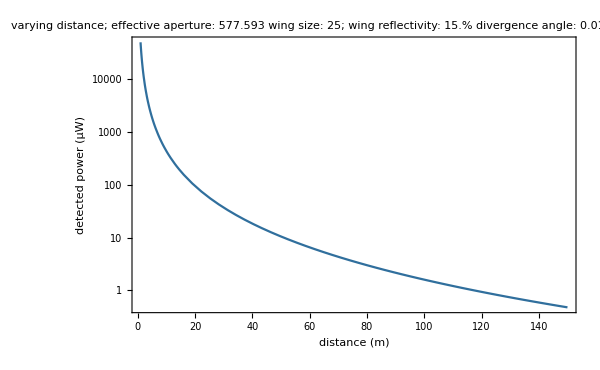

```mathematica
assignments={TelescopeOuterRadius->Quantity[tlr,"m"]/2,WingSize->UnitConvert[Quantity[ws,"mm^2"],"m^2"],RangeAtInsect-> Quantity[rng,"m"], Reflectivity-> Quantity[rlf,"DimensionlessUnit"], DivergenceAngle-> Quantity[da,"Radians"],Diffusivity->Quantity[difu,"sr"]};vals={tlr->.3048,rlf->.15,ws->25,da->0.0002,difu->Pi};
plt[1]=LogPlot[UnitConvert[DetectedPower/.assignments/.vals,"microWatts"],{rng,1,150},PlotLabel->StringJoin["varying distance; effective aperture: ",ToString[UnitConvert[EffectiveAperture/.assignments/.vals,"cm^2"],TraditionalForm],"\nwing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"; wing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm]," or ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"rad"],TraditionalForm]], FrameLabel->{"distance (m)","detected power (μW)"},PlotStyle->{c[1]}]
```

## vary effective aperture

```mathematica
ClearAll[tp,cv]
cv=1;
vals={da->.0002,rlf->.15,ws->25,lb->0.15,ub->.5,it->.075,difu->Pi};
Do[{tp[cv]=LogPlot[UnitConvert[DetectedPower/.assignments/.vals,"microWatts"],{rng,rangelb,rangeub},PlotStyle->{c[cv]}],cv=cv+1},{tlr,lb/.vals,ub/.vals,it/.vals}];
```

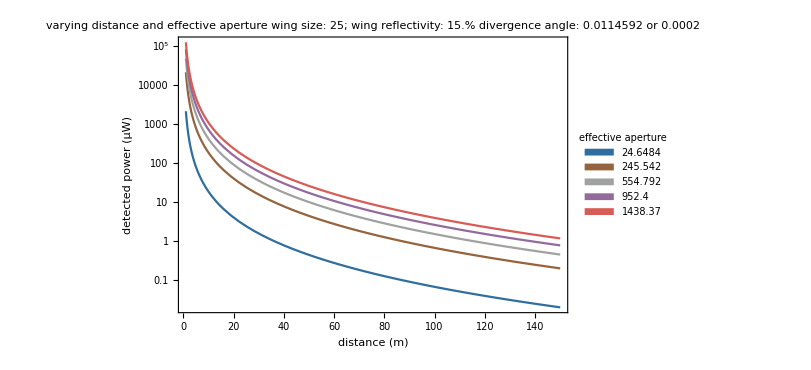

```mathematica
plt[2]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,FrameLabel->{"distance (m)","detected power (μW)"},PlotLabel->StringJoin["varying distance and effective aperture\nwing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"; wing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm]," or ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"rad"],TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[EffectiveAperture/.assignments/.vals,"cm^2"],TraditionalForm],{tlr,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"effective aperture"]]
```

## vary effective aperture

```mathematica
ClearAll[tp,cv]
cv=1;
vals={da->.0002,rlf->.15,ws->25,lb->0.15,ub->.5,it->.075,difu->Pi};
Do[{tp[cv]=Plot[UnitConvert[DetectedPower/.assignments/.vals,"microWatts"],{rng,rangelb,rangeub},PlotRange->{{0,150},{0,120}},PlotStyle->{c[cv]}],cv=cv+1},{tlr,lb/.vals,ub/.vals,it/.vals}];
```

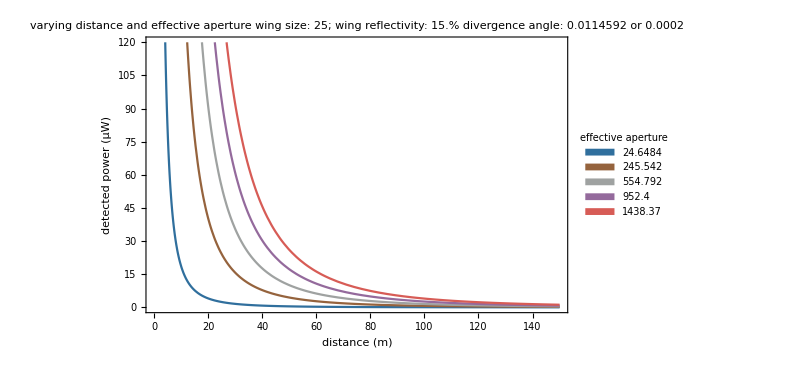

```mathematica
plt[22]=Legended[Show[Table[tp[h],{h,1,cv-1}],FrameLabel->{"distance (m)","detected power (μW)"},PlotLabel->StringJoin["varying distance and effective aperture\nwing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"; wing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm]," or ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"rad"],TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[EffectiveAperture/.assignments/.vals,"cm^2"],TraditionalForm],{tlr,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"effective aperture"]]
```

detected power vs effective aperture

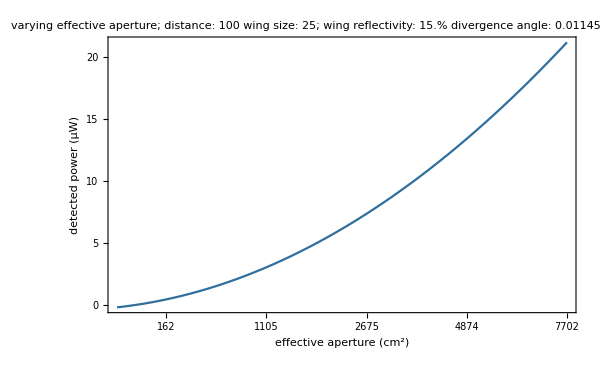

```mathematica
assignments={TelescopeOuterRadius->Quantity[tlr,"m"]/2,WingSize->UnitConvert[Quantity[ws,"mm^2"],"m^2"],RangeAtInsect-> Quantity[rng,"m"], Reflectivity-> Quantity[rlf,"DimensionlessUnit"], DivergenceAngle-> Quantity[da,"Radians"],Diffusivity->Quantity[difu,"sr"]};vals={rng->100,rlf->.15,ws->25,da->0.0002,difu->Pi};
plt[3]=Plot[UnitConvert[DetectedPower/.assignments/.vals,"microWatts"],{tlr,.1016,1},Frame->{{True,True},{True,True}},FrameTicks->{{All,None},{Table[{tlr,Round[QuantityMagnitude[UnitConvert[EffectiveAperture/.assignments,"cm^2"]]]},{tlr,.2,1,.2}],None}},PlotLabel->StringJoin["varying effective aperture; distance: ",ToString[UnitConvert[RangeAtInsect/.assignments/.vals,"m"],TraditionalForm],"\nwing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"; wing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm]," or ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"rad"],TraditionalForm]], FrameLabel->{"effective aperture (cm^2)","detected power (μW)"},PlotStyle->{c[1]}]
```

## vary distance

```mathematica
ClearAll[tp,cv]
cv=1;
vals={da->.0002,rlf->.15,ws->25,lb->11,ub->141,it->20,difu->Pi};
Do[{tp[cv]=Plot[Log10[QuantityMagnitude[UnitConvert[DetectedPower/.assignments/.vals,"microWatts"]]],{tlr,.1016,1},PlotStyle->{c[cv]}],cv=cv+1},{rng,lb/.vals,ub/.vals,it/.vals}];
```

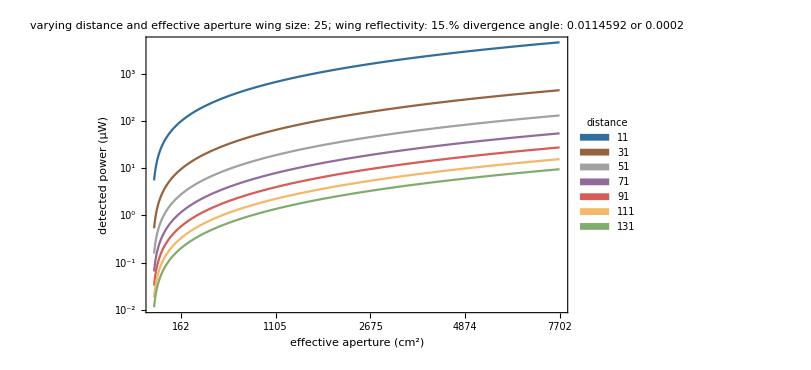

```mathematica
plt[4]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->Automatic,FrameLabel->{"effective aperture (cm^2)","detected power (μW)"},
FrameTicks->{{{#,Superscript[10,#]}&/@(Table[x,{x,-2,3}]),None},{Table[{tlr,Round[QuantityMagnitude[UnitConvert[EffectiveAperture/.assignments,"cm^2"]]]},{tlr,.2,1,.2}],None}},PlotLabel->StringJoin["varying distance and effective aperture\nwing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"; wing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm]," or ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"rad"],TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[RangeAtInsect/.assignments/.vals,"m"],TraditionalForm],{rng,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"distance"]]
```

## vary distance

```mathematica
ClearAll[tp,cv]
cv=1;
vals={da->.0002,rlf->.15,ws->25,lb->40,ub->130,it->15,difu->Pi};
Do[{tp[cv]=Plot[UnitConvert[DetectedPower/.assignments/.vals,"microWatts"],{tlr,.1016,1},PlotStyle->{c[cv]}],cv=cv+1},{rng,lb/.vals,ub/.vals,it/.vals}];
```

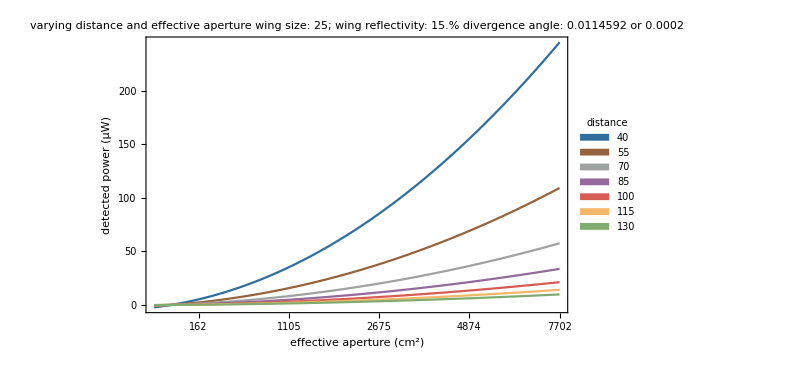

```mathematica
plt[21]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->Automatic,FrameLabel->{"effective aperture (cm^2)","detected power (μW)"},PlotRange->{{0,1},{0,300}},FrameTicks->{{{#,#}&/@(Table[x,{x,0,300,50}]),None},{Table[{tlr,Round[QuantityMagnitude[UnitConvert[EffectiveAperture/.assignments,"cm^2"]]]},{tlr,.2,1,.2}],None}},PlotLabel->StringJoin["varying distance and effective aperture\nwing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"; wing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm]," or ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"rad"],TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[RangeAtInsect/.assignments/.vals,"m"],TraditionalForm],{rng,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"distance"]]
```

SNR vs distance

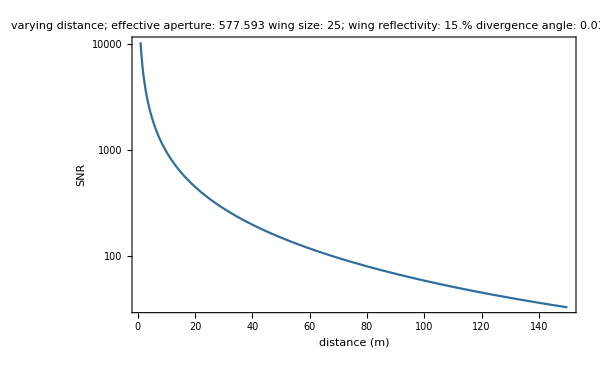

```mathematica
assignments={TelescopeOuterRadius->Quantity[tlr,"m"]/2,WingSize->UnitConvert[Quantity[ws,"mm^2"],"m^2"],RangeAtInsect-> Quantity[rng,"m"], Reflectivity-> Quantity[rlf,"DimensionlessUnit"], DivergenceAngle-> Quantity[da,"Radians"],Diffusivity->Quantity[difu,"sr"]};vals={tlr->.3048,rlf->.15,ws->25,da->0.0002,difu->Pi};
plt[5]=LogPlot[UnitConvert[SNR/.assignments/.vals,"DimensionlessUnit"],{rng,1,150},PlotLabel->StringJoin["varying distance; effective aperture: ",ToString[UnitConvert[EffectiveAperture/.assignments/.vals,"cm^2"],TraditionalForm],"\nwing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"; wing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm]," or ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"rad"],TraditionalForm]], FrameLabel->{"distance (m)","SNR"},PlotStyle->{c[1]}]
```

## vary effective aperture

```mathematica
ClearAll[tp,cv]
cv=1;
vals={da->.0002,rlf->.15,ws->25,lb->0.15,ub->.5,it->.075,difu->Pi};
Do[{tp[cv]=LogPlot[UnitConvert[SNR/.assignments/.vals,"DimensionlessUnit"],{rng,rangelb,rangeub},PlotStyle->{c[cv]}],cv=cv+1},{tlr,lb/.vals,ub/.vals,it/.vals}];
```

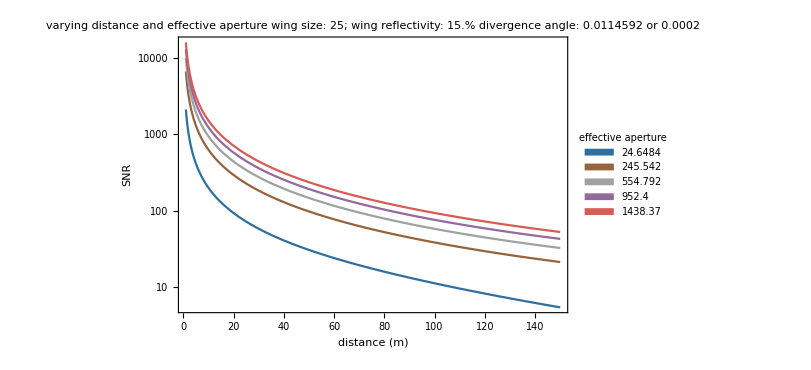

```mathematica
plt[6]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,FrameLabel->{"distance (m)","SNR"},PlotLabel->StringJoin["varying distance and effective aperture\nwing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"; wing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm]," or ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"rad"],TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[EffectiveAperture/.assignments/.vals,"cm^2"],TraditionalForm],{tlr,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"effective aperture"]]
```

SNR vs effective aperture

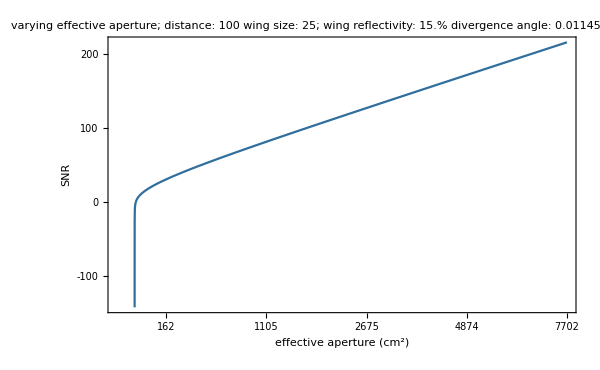

```mathematica
assignments={TelescopeOuterRadius->Quantity[tlr,"m"]/2,WingSize->UnitConvert[Quantity[ws,"mm^2"],"m^2"],RangeAtInsect-> Quantity[rng,"m"], Reflectivity-> Quantity[rlf,"DimensionlessUnit"], DivergenceAngle-> Quantity[da,"Radians"],Diffusivity->Quantity[difu,"sr"]};vals={rng->100,rlf->.15,ws->25,da->0.0002,difu->Pi};
plt[7]=Plot[UnitConvert[SNR/.assignments/.vals,"DimensionlessUnit"],{tlr,.1016,1},FrameTicks->{{All,None},{Table[{tlr,Round[QuantityMagnitude[UnitConvert[EffectiveAperture/.assignments,"cm^2"]]]},{tlr,.2,1,.2}],None}},PlotLabel->StringJoin["varying effective aperture; distance: ",ToString[UnitConvert[RangeAtInsect/.assignments/.vals,"m"],TraditionalForm],"\nwing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"; wing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm]," or ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"rad"],TraditionalForm]], FrameLabel->{"effective aperture (cm^2)","SNR"},PlotStyle->{c[1]}]
```

SNR vs divergence angle

```mathematica
ClearAll[tp,cv]
cv=1;
vals={rng->100,rlf->.15,ws->25,lb->.16,ub->.5,it->.075,difu->Pi};
Do[{tp[cv]=LogPlot[UnitConvert[SNR/.assignments/.vals,"DimensionlessUnit"],{da,0,.0004},PlotStyle->{c[cv]}],cv=cv+1},{tlr,lb/.vals,ub/.vals,it/.vals}];
```

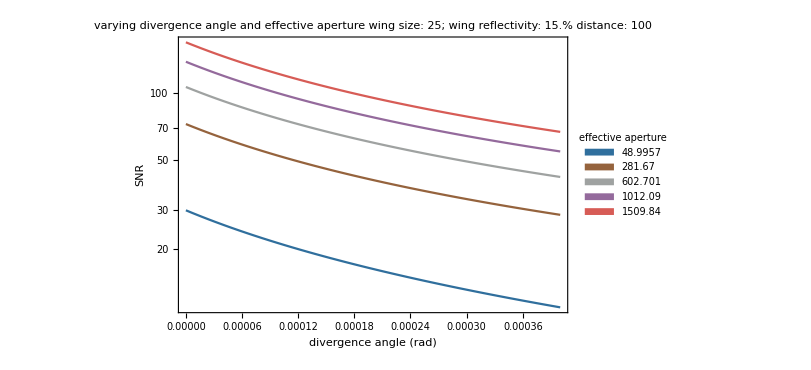

```mathematica
plt[8]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,FrameLabel->{"divergence angle (rad)","SNR"},PlotLabel->StringJoin["varying divergence angle and effective aperture\nwing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"; wing reflectivity: ",ToString[(Reflectivity/.assignments/.vals)*100,TraditionalForm],"% \ndistance: ",ToString[UnitConvert[RangeAtInsect/.assignments/.vals,"m"],TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[EffectiveAperture/.assignments/.vals,"cm^2"],TraditionalForm],{tlr,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"effective aperture"]]
```

# Set SNR Plots

Solve for TelescopeOuterRadius

```mathematica
assignments={WingSize->UnitConvert[Quantity[ws,"mm^2"],"m^2"],RangeAtInsect-> Quantity[rng,"m"], Reflectivity-> Quantity[rlf,"DimensionlessUnit"], DivergenceAngle-> Quantity[da,"Radians"],Diffusivity->Quantity[difu,"sr"]};
```

```mathematica
sol=Solve[SNR==SNRv/.assignments,TelescopeOuterRadius][[4]];
```

## vary distance

```mathematica
vals={rlf->.15,ws->25,da->.0002,cv->1,difu->Pi};
plt[9]=Plot[UnitConvert[EffectiveAperture/.sol/.vals,"cm^2"],{rng, rangelb, rangeub},PlotLabel->StringJoin["varying distance; wing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"\nwing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%; SNR: ",ToString[SNRv],";\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm], " or: ", ToString[DivergenceAngle/.assignments/.vals,TraditionalForm]],PlotStyle->{c[cv/.vals]},FrameLabel->{"distance (m)","telescope effective aperture (cm^2)"}]
```

General::munfl: 1/((2.10798×10^282)^2) is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

## vary divergence angle

```mathematica
ClearAll[tp,cv]
cv=1;
vals={rlf->.15,ws->25,lb->0,ub->.0004,it->.0001,difu->Pi};
Do[{tp[cv]=Plot[UnitConvert[EffectiveAperture/.sol/.vals,"cm^2"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","telescope effective aperture (cm^2)"}],cv=cv+1},{da,lb/.vals,ub/.vals,it/.vals}];
```

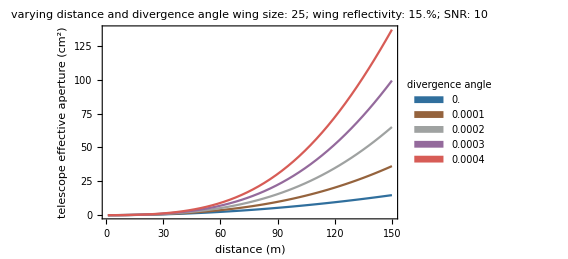

```mathematica
plt[10]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,PlotLabel->StringJoin["varying distance and divergence angle\nwing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"; wing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%; SNR: ",ToString[SNRv]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"rad"],TraditionalForm],{da,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"divergence angle"]]
```

## vary wing size

```mathematica
ClearAll[tp,cv]
cv=1;
vals={rlf->.15,da->.0002,lb->16,ub->106,it->15,difu->Pi};
Do[{tp[cv]=Plot[UnitConvert[EffectiveAperture/.sol/.vals,"cm^2"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","telescope effective aperture (cm^2)"}],cv=cv+1},{ws,lb/.vals,ub/.vals,it/.vals}];
```

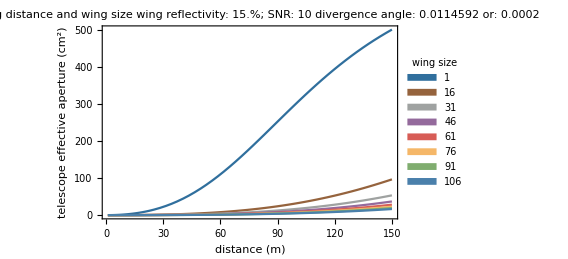

```mathematica
plt[11]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,PlotLabel->StringJoin["varying distance and wing size\n","wing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%; SNR: ",ToString[SNRv],"\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm], " or: ", ToString[DivergenceAngle/.assignments/.vals,TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],{ws,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"wing size"]]
```

## varying reflectivity

```mathematica
ClearAll[tp,cv]
cv=1;
vals={ws->25,da->.0002,lb->.01,ub->1.0,it->.12,difu->Pi};
Do[{tp[cv]=Plot[UnitConvert[EffectiveAperture/.sol/.vals,"cm^2"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","telescope effective aperture (cm^2)"}],cv=cv+1},{rlf,lb/.vals,ub/.vals,it/.vals}];
```

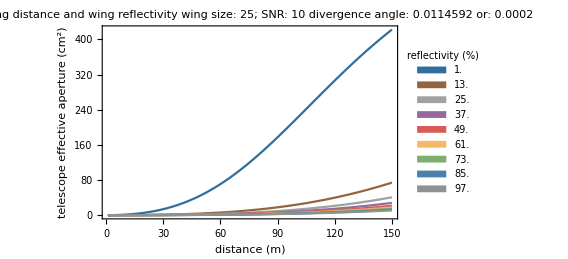

```mathematica
plt[12]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,PlotLabel->StringJoin["varying distance and wing reflectivity\n","wing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"; SNR: ",ToString[SNRv],"\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm], " or: ", ToString[DivergenceAngle/.assignments/.vals,TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[(Reflectivity/.assignments/.vals)*100,"DimensionlessUnit"],TraditionalForm],{rlf,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"reflectivity (%)"]]
```

Solve for WingSize

```mathematica
assignments={TelescopeOuterRadius->Quantity[tlr,"m"]/2,RangeAtInsect-> Quantity[rng,"m"], Reflectivity-> Quantity[rlf,"DimensionlessUnit"], DivergenceAngle-> Quantity[da,"Radians"],Diffusivity->Quantity[difu,"sr"]};
```

```mathematica
sol=Solve[SNR==SNRv/.assignments,WingSize][[2]];
```

## varying distance

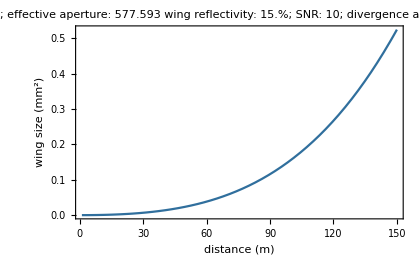

```mathematica
vals={da->.0002,rlf->.15,tlr->.3048,difu->Pi};
plt[13]=Plot[UnitConvert[WingSize/.sol/.vals,"mm^2"],{rng,rangelb,rangeub},PlotLabel->StringJoin["varying distance; effective aperture: ",ToString[UnitConvert[EffectiveAperture/.assignments/.vals,"cm^2"],TraditionalForm],"\nwing reflectivity: ",ToString[(100*Reflectivity/.assignments/.vals),TraditionalForm],"%; SNR: ",ToString[SNRv],";\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm], " or: ", ToString[DivergenceAngle/.assignments/.vals,TraditionalForm]],PlotStyle->{c[1]},FrameLabel->{"distance (m)","wing size (mm^2)"}]
```

## varying divergence angle

```mathematica
ClearAll[tp,cv]
cv=1;
vals={tlr->.3048,rlf->.15,lb->.0,ub->.0004,it->.0001,difu->Pi};
Do[{tp[cv]=LogPlot[UnitConvert[WingSize/.sol/.vals,"mm^2"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","wing size (mm^2)"},RotateLabel->False],cv=cv+1},{da,lb/.vals,ub/.vals,it/.vals}];
```

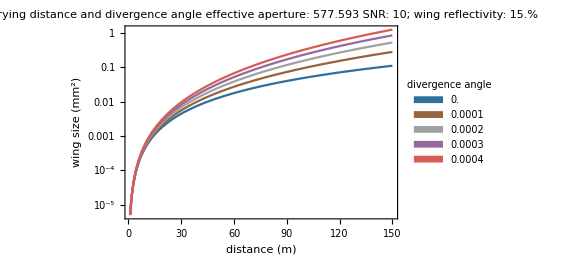

```mathematica
plt[14]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,PlotLabel->StringJoin["varying distance and divergence angle\n","effective aperture: ",ToString[UnitConvert[EffectiveAperture/.assignments/.vals,"cm^2"],TraditionalForm],"\nSNR: ",ToString[SNRv],"; wing reflectivity: ",ToString[(Reflectivity/.assignments/.vals)*100,TraditionalForm],"%"]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"Radians"],TraditionalForm],{da,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"divergence angle"]]
```

## varying reflectivity

```mathematica
ClearAll[tp,cv]
cv=1;
vals={tlr->.3048,da->.0002,lb->.01,ub->1.0,it->.12,difu->Pi};
Do[{tp[cv]=LogPlot[UnitConvert[WingSize/.sol/.vals,"mm^2"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","wing size (mm^2)"}],cv=cv+1},{rlf,lb/.vals,ub/.vals,it/.vals}];
```

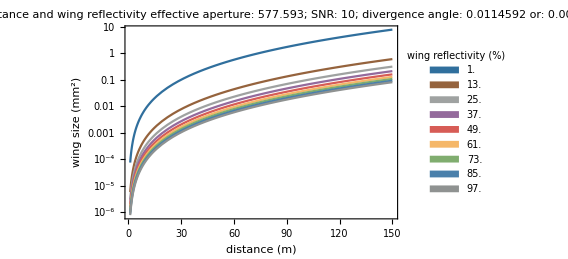

```mathematica
plt[15]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,PlotLabel->StringJoin["varying distance and wing reflectivity\n","effective aperture: ",ToString[UnitConvert[EffectiveAperture/.assignments/.vals,"cm^2"],TraditionalForm],"; SNR: ",ToString[SNRv],";\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm], " or: ", ToString[DivergenceAngle/.assignments/.vals,TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[(Reflectivity/.assignments/.vals)*100,"DimensionlessUnit"],TraditionalForm],{rlf,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"wing reflectivity (%)"]]
```

## varying effective aperture

```mathematica
ClearAll[tp,cv]
cv=1;
vals={rlf->.15,da->.0002,lb->.15,ub->.5,it->.075,difu->Pi};
Do[{tp[cv]=LogPlot[UnitConvert[WingSize/.sol/.vals,"mm^2"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","wing size (mm^2)"}],cv=cv+1},{tlr,lb/.vals,ub/.vals,it/.vals}];
```

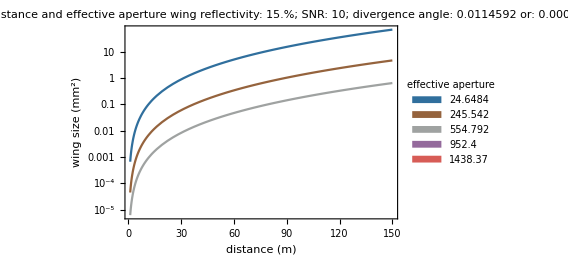

```mathematica
plt[16]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,PlotLabel->StringJoin["varying distance and effective aperture\nwing reflectivity: ",ToString[UnitConvert[(Reflectivity/.assignments/.vals)*100,"DimensionlessUnit"],TraditionalForm],"%; SNR: ",ToString[SNRv],";\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm], " or: ", ToString[DivergenceAngle/.assignments/.vals,TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[(EffectiveAperture/.assignments/.vals),"cm^2"],TraditionalForm],{tlr,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"effective aperture"]]
```

## Special Plots

```mathematica
ClearAll[tp,cv]
cv=1;
vals={tlr->.3048,rlf->.15,lb->.0,ub->.0004,it->.0001,difu->Pi};
Do[{tp[cv]=LogPlot[UnitConvert[WingSize/.sol/.vals,"mm^2"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","wing size (mm^2)"},RotateLabel->False],cv=cv+1},{da,lb/.vals,ub/.vals,it/.vals}];
```

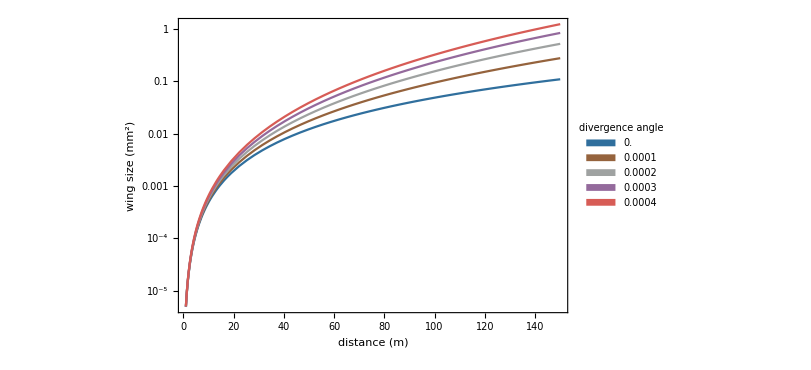

```mathematica
plt[14]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"Milliradians"],TraditionalForm],{da,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"divergence angle"]]
```

```mathematica
Export["D:\\insect_lidar\\Radiometric Analysis\\figures\\tel_ws.png",plt[11],ImageResolution->600]
```

D:\insect_lidar\Radiometric Analysis\figures\tel_ws.png

```mathematica
ClearAll[tp,cv]
cv=1;
vals={tlr->.3048,da->.0002,lb->.01,ub->1.0,it->.12,difu->Pi};
Do[{tp[cv]=LogPlot[UnitConvert[WingSize/.sol/.vals,"mm^2"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","wing size (mm^2)"},RotateLabel->False],cv=cv+1},{rlf,lb/.vals,ub/.vals,it/.vals}];
```

```mathematica
plt[15]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[(Reflectivity/.assignments/.vals)*100,"DimensionlessUnit"],TraditionalForm],{rlf,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"wing reflectivity (%)"]]
```

```mathematica
ClearAll[tp,cv]
cv=1;
vals={rlf->.15,da->.0002,lb->16,ub->106,it->15,difu->Pi};
Do[{tp[cv]=Plot[UnitConvert[EffectiveAperture/.sol/.vals,"cm^2"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","telescope effective\naperture (cm^2)"},RotateLabel->False],cv=cv+1},{ws,lb/.vals,ub/.vals,it/.vals}];
```

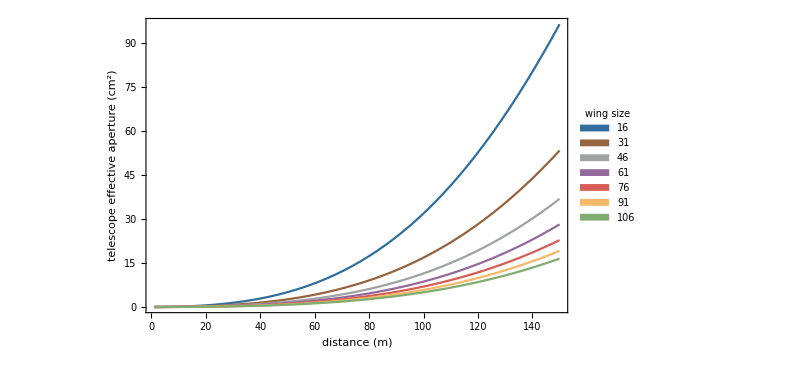

```mathematica
plt[11]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],{ws,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"wing size"]]
```

Solve for Wing Reflectivity

```mathematica
assignments={TelescopeOuterRadius->Quantity[tlr,"m"]/2,RangeAtInsect-> Quantity[rng,"m"], DivergenceAngle-> Quantity[da,"Radians"], WingSize->UnitConvert[Quantity[ws,"mm^2"],"m^2"],Diffusivity->Quantity[difu,"sr"]};
```

```mathematica
sol=Solve[SNR==SNRv/.assignments,Reflectivity][[2]];
```

## varying distance

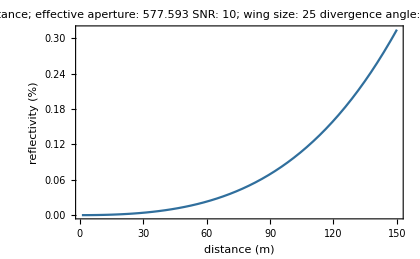

```mathematica
vals={ws->25,da->.0002,tlr->.3048,difu->Pi};
plt[17]=Plot[UnitConvert[(Reflectivity/.sol/.vals)*100,"DimensionlessUnit"],{rng,rangelb,rangeub},PlotLabel->StringJoin["varying distance; effective aperture: ",ToString[UnitConvert[EffectiveAperture/.assignments/.vals,"cm^2"],TraditionalForm],"\nSNR: ",ToString[SNRv],"; wing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm],"\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm], " or: ", ToString[DivergenceAngle/.assignments/.vals,TraditionalForm]],PlotStyle->{c[1]},FrameLabel->{"distance (m)","reflectivity (%)"}]
```

## varying effective aperture

```mathematica
ClearAll[tp,cv]
cv=1;
vals={ws->25,da->.0002,lb->.2,ub->.5,it->.075,difu->Pi};
Do[{tp[cv]=Plot[UnitConvert[(Reflectivity/.sol/.vals)*100,"DimensionlessUnit"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","reflectivity (%)"}],cv=cv+1},{tlr,lb/.vals,ub/.vals,it/.vals}];
```

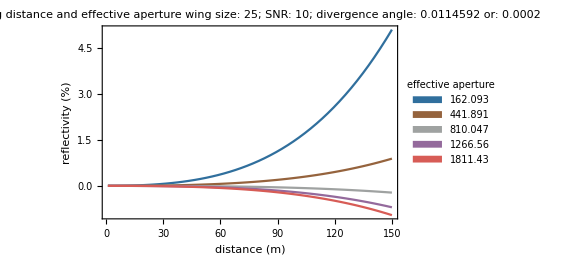

```mathematica
plt[18]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,PlotLabel->StringJoin["varying distance and effective aperture\nwing size: ",ToString[UnitConvert[(WingSize/.assignments/.vals),"mm^2"],TraditionalForm],"; SNR: ",ToString[SNRv],";\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm], " or: ", ToString[DivergenceAngle/.assignments/.vals,TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[(EffectiveAperture/.assignments/.vals),"cm^2"],TraditionalForm],{tlr,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"effective aperture"]]
```

## varying wing size

```mathematica
ClearAll[tp,cv]
cv=1;
vals={tlr->.3048,da->.0002,lb->1,ub->106,it->15,difu->Pi};
Do[{tp[cv]=Plot[UnitConvert[(Reflectivity/.sol/.vals)*100,"DimensionlessUnit"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","reflectivity (%)"}],cv=cv+1},{ws,lb/.vals,ub/.vals,it/.vals}];
```

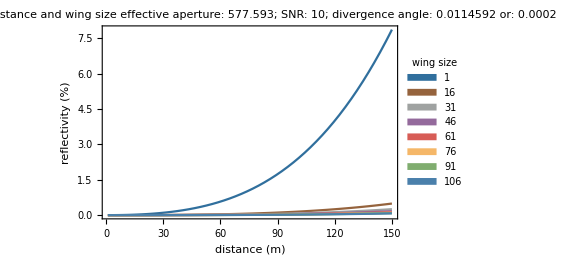

```mathematica
plt[19]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,PlotLabel->StringJoin["varying distance and wing size\neffective aperture: ",ToString[UnitConvert[(EffectiveAperture/.assignments/.vals),"cm^2"],TraditionalForm],"; SNR: ",ToString[SNRv],";\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm], " or: ", ToString[DivergenceAngle/.assignments/.vals,TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[(WingSize/.assignments/.vals),"mm^2"],TraditionalForm],{ws,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"wing size"]]
```

## varying wing size log

```mathematica
ClearAll[tp,cv]
cv=1;
vals={tlr->.3048,da->.0002,lb->1,ub->106,it->15,difu->Pi};
Do[{tp[cv]=LogPlot[UnitConvert[(Reflectivity/.sol/.vals)*100,"DimensionlessUnit"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","reflectivity (%)"}],cv=cv+1},{ws,lb/.vals,ub/.vals,it/.vals}];
```

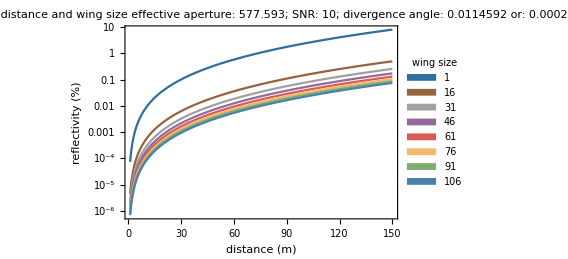

```mathematica
plt[23]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,PlotLabel->StringJoin["varying distance and wing size\neffective aperture: ",ToString[UnitConvert[(EffectiveAperture/.assignments/.vals),"cm^2"],TraditionalForm],"; SNR: ",ToString[SNRv],";\ndivergence angle: ",ToString[UnitConvert[DivergenceAngle/.assignments/.vals,"degrees"],TraditionalForm], " or: ", ToString[DivergenceAngle/.assignments/.vals,TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[(WingSize/.assignments/.vals),"mm^2"],TraditionalForm],{ws,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"wing size"]]
```

## varying divergence angle

```mathematica
ClearAll[tp,cv]
cv=1;
vals={tlr->.3048,ws->25,lb->0,ub->.0004,it->.0001,difu->Pi};
Do[{tp[cv]=Plot[UnitConvert[(Reflectivity/.sol/.vals)*100,"DimensionlessUnit"],{rng,rangelb,rangeub},PlotStyle->{c[cv]},FrameLabel->{"distance (m)","reflectivity (%)"}],cv=cv+1},{da,lb/.vals,ub/.vals,it/.vals}];
```

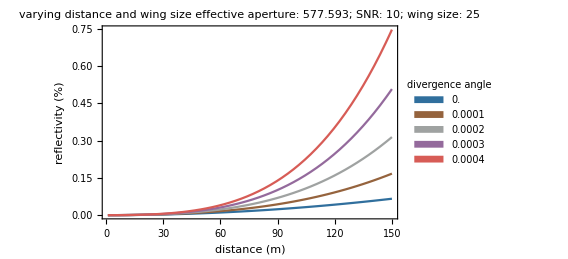

```mathematica
plt[20]=Legended[Show[Table[tp[h],{h,1,cv-1}],PlotRange->All,PlotLabel->StringJoin["varying distance and wing size\neffective aperture: ",ToString[UnitConvert[(EffectiveAperture/.assignments/.vals),"cm^2"],TraditionalForm],"; SNR: ",ToString[SNRv],";\nwing size: ",ToString[UnitConvert[WingSize/.assignments/.vals,"mm^2"],TraditionalForm]]],SwatchLegend[Table[c[x],{x,1,cv-1}],Table[ToString[UnitConvert[(DivergenceAngle/.assignments/.vals),"radians"],TraditionalForm],{da,lb/.vals,ub/.vals,it/.vals}],LegendLabel->"divergence angle"]]
```

Solve for Wing Diffusivity

```mathematica
assignments={TelescopeOuterRadius->Quantity[tlr,"m"]/2,RangeAtInsect-> Quantity[rng,"m"], DivergenceAngle-> Quantity[da,"Radians"], WingSize->UnitConvert[Quantity[ws,"mm^2"],"m^2"],Reflectivity->Quantity[rlf,"DimensionlessUnit"]};
```

```mathematica
sol=Solve[SNR==SNRv/.assignments,Diffusivity][[1]];
```

$Aborted

# Eye Safety

```mathematica
assignments={TelescopeOuterRadius->Quantity[tlr,"m"]/2,RangeAtInsect-> Quantity[rng,"m"], Reflectivity-> Quantity[rlf,"DimensionlessUnit"], DivergenceAngle-> Quantity[da,"Radians"],WingSize->Quantity[ws,"mm^2"]};
vals={tlr->.3048,ws->25,rng->100,rlf->.15,da->.0002};
```

```mathematica
{tlr->0.3048,ws->25,rng->100,rlf->0.15,da->0.0002}
```

{tlr→0.3048,ws→25,rng→100,rlf→0.15,da→0.0002}

```mathematica
pulsereprate=Quantity[9,"kHz"]
```

9 kHz

```mathematica
Time=Quantity[0.25,"s"]
```

0.25 s

```mathematica
MPE=Quantity[1.8*Time^(3/4)/Quantity[1,"s^(3/4)"]*10^-3,"J/cm^2"]
```

0.000636396 J/cm^2

```mathematica
n=UnitConvert[pulsereprate*Time,"DimensionlessUnit"]
```

2250.

```mathematica
Cp=n^(-1/4)
```

0.145196

```mathematica
MPEwCp=ScientificForm[MPE*Cp]
```

9.24021×10^-5 J/cm^2

```mathematica
MPEwCW=MPE/n//N
```

2.82843×10^-7 J/cm^2

```mathematica
ES=UnitConvert[LaserEnergy/(((BeamDiameter/.assignments/.vals)/2)^2*Pi),"J/cm^2"]
```

4.63297×10^-8 J/cm^2

Note that ES < MPEwCW ⇒ eye safety

# Overlap

Telescope FOV

```mathematica
x=3.7;
y=13.0;
EPL=4+635+631+660+17.391+11.740+20.0+5.34+46.112
```

2030.58

```mathematica
FOVx=ArcTan[(x/2)/EPL]
FOVy=ArcTan[(y/2)/EPL]
FOVd=ArcTan[Sqrt[(x/2)^2+(y/2)^2]/EPL]
```

0.000911068

0.00320104

0.00332817

```mathematica
50.8*Tan[Quantity[Pi/2-FOVd,"radians"]]
```

15263.6

```mathematica
25.4/(Tan[Quantity[FOVd,"radians"]]+Tan[Quantity[.0002,"radians"]])
```

7199.18

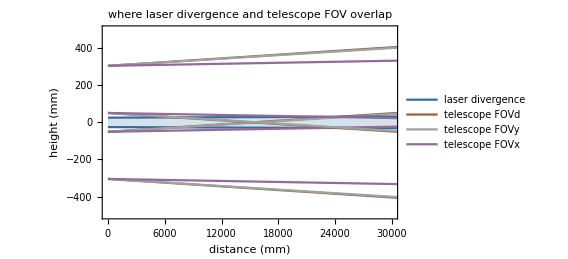

```mathematica
plt[25]=Plot[{(Tan[-0.0002]*xt)-25.4,(Tan[FOVd]*xt)-50.8,(Tan[FOVy]*xt)-50.8,(Tan[FOVx]*xt)-50.8,(Tan[0.0002]*xt)+25.4,(Tan[-FOVd]*xt)+50.8,(Tan[-FOVy]*xt)+50.8,(Tan[-FOVx]*xt)+50.8,(Tan[-FOVd]*xt)-304.8,(Tan[-FOVy]*xt)-304.8,(Tan[-FOVx]*xt)-304.8,(Tan[FOVd]*xt)+304.8,(Tan[FOVy]*xt)+304.8,(Tan[FOVx]*xt)+304.8},{xt,0,50000},PlotStyle->{c[1],c[2],c[3],c[4],c[1],c[2],c[3],c[4],c[2],c[3],c[4],c[2],c[3],c[4]},FrameLabel->{"distance (mm)","height (mm)"},Filling->{1->{5}},PlotRange->{{0,30000},{-500,500}},PlotLegends->{"laser divergence","telescope FOVd","telescope FOVy","telescope FOVx"},PlotLabel->"where laser divergence and telescope FOV overlap"]
```

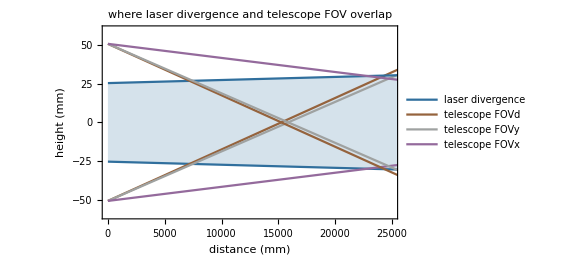

```mathematica
plt[24]=Plot[{(Tan[-0.0002]*xt)-25.4,(Tan[FOVd]*xt)-50.8,(Tan[FOVy]*xt)-50.8,(Tan[FOVx]*xt)-50.8,(Tan[0.0002]*xt)+25.4,(Tan[-FOVd]*xt)+50.8,(Tan[-FOVy]*xt)+50.8,(Tan[-FOVx]*xt)+50.8,(Tan[-FOVd]*xt)-304.8,(Tan[-FOVy]*xt)-304.8,(Tan[-FOVx]*xt)-304.8,(Tan[FOVd]*xt)+304.8,(Tan[FOVy]*xt)+304.8,(Tan[FOVx]*xt)+304.8},{xt,0,50000},PlotStyle->{c[1],c[2],c[3],c[4],c[1],c[2],c[3],c[4],c[2],c[3],c[4],c[2],c[3],c[4]},PlotRange->{{0,25000},{-60,60}},FrameLabel->{"distance (mm)","height (mm)"},Filling->{1->{5}},PlotLegends->{"laser divergence","telescope FOVd","telescope FOVy","telescope FOVx"},PlotLabel->"where laser divergence and telescope FOV overlap"]
```

# save

```mathematica
(*Do[Export[fullfilecld<>"plt"<>ToString[x]<>".png",plt[x]],{x,1,25,1}];
Do[Export[fullfileloc<>"plt"<>ToString[x]<>".png",plt[x]],{x,1,25,1}];*)
```